## DTissue-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Cellzilla2D (3.0.51 (05 June 2017)) loaded Wed 7 Jun 2017 14:21:30
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

There are 14 cells in the tissue.

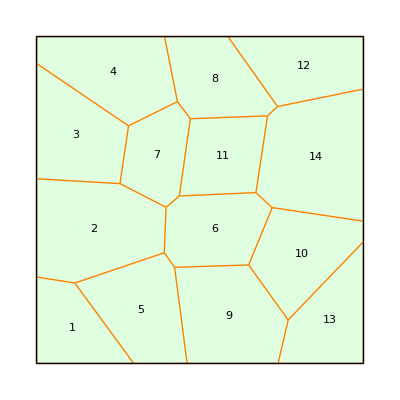

```mathematica
q=TemplateRandomSquareGrid[12, {-50, -50}, {50, 50}];
Q=Tissue2DTissue[q]; 
Print["There are ", NTissueCells[Q], " cells in the tissue."];  
ShowTissue[Q, "CellNumbers"-> True, Frame-> False, "EdgeStyles"-> Directive[Orange,Thick]]
```

```mathematica
Q
```

DTissue[{{-38.295,-25.3934},{-24.4769,5.02082},{-21.8585,22.6786},{-10.9342,-16.1372},{-10.3795,-2.23875},{-7.77269,-20.5816},{-6.89887,30.0918},{-6.33332,1.23278},{-2.93998,24.8576},{14.8847,-19.8801},{17.107,2.25663},{20.6655,25.734},{22.0756,-2.32667},{23.7214,28.5833},{26.9725,-36.6911},{50,-50},{50,50},{-50,50},{-50,-50},{50.,-12.748},{50.,-6.48407},{50.,33.9311},{8.54103,50.},{-10.8547,50.},{-50.,41.7726},{-50.,6.48625},{-50.,-23.5494},{-20.2739,-50.},{-3.9389,-50.},{23.874,-50.}},{{1,4},{1,27},{1,28},{2,3},{2,5},{2,26},{3,7},{3,25},{4,5},{4,6},{5,8},{6,10},{6,29},{7,9},{7,24},{8,9},{8,11},{9,12},{10,13},{10,15},{11,12},{11,13},{12,14},{13,21},{14,22},{14,23},{15,20},{15,30},{16,20},{16,30},{17,22},{17,23},{18,24},{18,25},{19,27},{19,28},{20,21},{21,22},{23,24},{25,26},{26,27},{28,29},{29,30}},{1→{36,3,2,35},2→{41,2,1,9,5,6},3→{40,6,4,8},4→{34,8,7,15,33},5→{42,13,10,1,3},6→{11,9,10,12,19,22,17},7→{5,11,16,14,7,4},8→{39,15,14,18,23,26},9→{43,28,20,12,13},10→{37,24,19,20,27},11→{16,17,21,18},12→{32,26,25,31},13→{27,28,30,29},14→{38,25,23,21,22,24}}]